# Пререшаване - Вариант 3, Задача 3, фак. номер 2001261003

a = 0, b = 3

## Съставяне на мрежата

```mathematica
f[x_]:=(-90Cos[x] + x^3  + 23)/(5 - x^2)
a = 0.; b = 3;
h = 0.3;
xt = Table[13 + i*h, {i,0,10}]
```

{13.,13.3,13.6,13.9,14.2,14.5,14.8,15.1,15.4,15.7,16.}

```mathematica
f[xt]
```

{-13.0386,-13.4318,-13.8498,-14.2791,-14.7068,-15.1209,-15.5119,-15.8729,-16.2002,-16.493,-16.7537}

## Леви правоъгълници

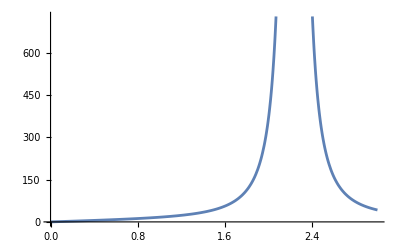

```mathematica
Plot[Abs[f'[x]],{x,a,b}]
```

```mathematica
a = 6.;b= 7.;
h = 0.3;
n = (b-a)/h;
f[x_]:= (-360Cos[x] + x^3  + 23)/(9 - x^2)
Itochno = ∫_a^b f[x]ⅆx ;
I1 = h*∑_(i=0)^(n-1) f[a+i*h];
M1 = Abs[f'[a]];
R1 = (b-a)^2/(2n)*M1;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на левите правоъгълници е ", I1]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R1]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I1-Itochno]]
```

Мрежата е със стъпка 0.3 и брой подинтервали 3.33333

Приближената стойност по формулата на левите правоъгълници е 2.30881

Точната стойност                                           е 1.34742

Теоретичната грешка по формулата на левите правоъгълници   е 0.30453

Истинската грешка по формулата на левите правоъгълници     е 0.961384

## Колко ще са подинтервалите за достигане на точност 0.000001 със същия подход

## Леви правоъгълници

```mathematica
eps = 10^-6;
Clear[n]
Reduce[(b-a)^2/(2n)*M1<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥1.0151×10^6

```mathematica
a = 6.;b= 7;
n = 10^6;
h = (b -a)/n;
f[x_]:= (9-x)/(2 x^2 + 7)
Itochno = ∫_a^b f[x]ⅆx ;
I1 = h*∑_(i=0)^(n-1) f[a+i*h];
M1 = Abs[f'[a]];
R1 = (b-a)^2/(2n)*M1;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n] 
Print["Приближената стойност по формулата на левите правоъгълници е ", I1]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R1]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I1-Itochno]]
```

Мрежата е със стъпка 1.×10^-6 и брой подинтервали 1000000

Приближената стойност по формулата на левите правоъгълници е 0.0277173

Точната стойност                                           е 0.0277173

Теоретичната грешка по формулата на левите правоъгълници   е 1.20974×10^-8

Истинската грешка по формулата на левите правоъгълници     е 9.82472×10^-9

## Симпсън

Може да използваме формулата на Симпсън, тъй като броят на подинтервалите е четно число - в случая 12.

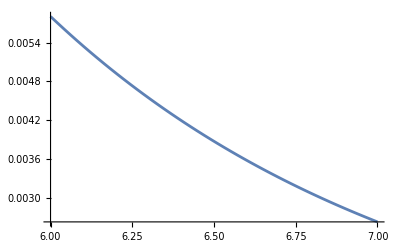

```mathematica
Plot[Abs[f''''[x]],{x,a,b}]
```

```mathematica
a = 6.;b= 14.;
h = (b -a)/n;
n = 12;
f[x_]:= (9-x)/(2 x^2 + 7)
Itochno = ∫_a^b f[x]ⅆx ;
m = n /2;
IS = h/3*(f[a]+4∑_(i=1)^m f[a+(2i-1)*h]+2∑_(i=1)^(m-1) f[a+(2i)*h]+f[b]);
M4 = Abs[f''''[a]];
RS = (b-a)^5/(180 n^4)*M4;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на Симпсън  е ", IS]
Print["Точната стойност                               е ", Itochno]
Print["Теоретичната грешка по формулата на Симпсън    е ", RS]
Print["Истинската грешка по формулата на Симпсън      е ", Abs[IS-Itochno]]
```

Мрежата е със стъпка 8.×10^-6 и брой подинтервали 12

Приближената стойност по формулата на Симпсън  е 3.51078×10^-6

Точната стойност                               е 0.00260677

Теоретичната грешка по формулата на Симпсън    е 0.0000509523

Истинската грешка по формулата на Симпсън      е 0.00260326

## Леви правоъгълници

```mathematica
eps = 10^-6;
Clear[n]
Reduce[(b-a)^2/(2n)*M1<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥774235.

```mathematica
a = 6.;b= 7;
n = 10^6;
h = (b -a)/n;
f[x_]:= (9-x)/(2 x^2 + 7)
Itochno = ∫_a^b f[x]ⅆx ;
I1 = h*∑_(i=0)^(n-1) f[a+i*h];
M1 = Abs[f'[a]];
R1 = (b-a)^2/(2n)*M1;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n] 
Print["Приближената стойност по формулата на левите правоъгълници е ", I1]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R1]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I1-Itochno]]
```

Мрежата е със стъпка 1.×10^-6 и брой подинтервали 1000000

Приближената стойност по формулата на левите правоъгълници е 0.0277173

Точната стойност                                           е 0.0277173

Теоретичната грешка по формулата на левите правоъгълници   е 1.20974×10^-8

Истинската грешка по формулата на левите правоъгълници     е 9.82472×10^-9

## Симпсън

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^5/(180 n^4)*M4<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-1.34002||n≥1.34002

```mathematica
a = 6.;b= 14.;
n = 19;
h = (b -a)/n;
f[x_]:= (9-x)/(2 x^2 + 7)
Itochno = ∫_a^b f[x]ⅆx ;
m = n /2;
IS = h/3*(f[a]+4∑_(i=1)^m f[a+(2i-1)*h]+2∑_(i=1)^(m-1) f[a+(2i)*h]+f[b]);
M4 = Abs[f''''[a]];
RS = (b-a)^5/(180 n^4)*M4;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на Симпсън  е ", IS]
Print["Точната стойност                               е ", Itochno]
Print["Теоретичната грешка по формулата на Симпсън    е ", RS]
Print["Истинската грешка по формулата на Симпсън      е ", Abs[IS-Itochno]]
```

Мрежата е със стъпка 0.421053 и брой подинтервали 19

Приближената стойност по формулата на Симпсън  е 0.00776531

Точната стойност                               е 0.00260677

Теоретичната грешка по формулата на Симпсън    е 8.10727×10^-6

Истинската грешка по формулата на Симпсън      е 0.00515854